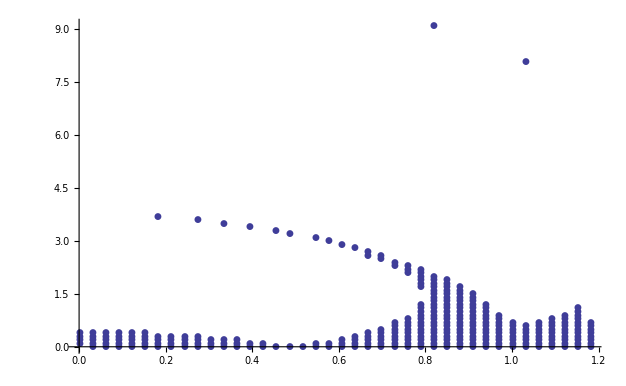

```mathematica
μ=0.05;
eq={x''[t]+2*μ*β*x'[t]+(β^2+ϵ*Cos[t])x[t]==0};
arr=Array[{0,0}#&,10000];
cnt=0;
myTable=Table[
{
Clear[β];
Clear[ϵ];
β=N[(i-1)/33];
ϵ=N[(j-1)/10];
a=First[x/.NDSolve[{x''[t]+2*μ*β*x'[t]+(β^2+ϵ*Cos[t])x[t]==0,x[0]==1,x'[0]==0},x,{t,0,4*Pi}]];
b=First[x/.NDSolve[{x''[t]+2*μ*β*x'[t]+(β^2+ϵ*Cos[t])x[t]==0,x[0]==0,x'[0]==1},x,{t,0,4*Pi}]];
eig=Eigenvalues[{{a[2*Pi],b[2*Pi]},{a'[2*Pi],b'[2*Pi]}}];
isStable={Abs[eig[[1]]]<1  && Abs[eig[[2]]]<1};
If[isStable[[1]],
{
cnt=cnt+1,
arr[[cnt]]={β,ϵ}
}
];
},
{i,100},{j,100}
]
ListPlot[arr,PlotRange->All,AxesLabel->{"β","ϵ"},PlotMarkers->Automatic]
```

```mathematica
μ=0.05
β=0.75
ϵ=2
a=First[x/.NDSolve[{x''[t]+2*μ*β*x'[t]+(β^2+ϵ*Cos[t])x[t]==0,x[0]==1,x'[0]==0},x,{t,0,4*Pi}]]
b=First[x/.NDSolve[{x''[t]+2*μ*β*x'[t]+(β^2+ϵ*Cos[t])x[t]==0,x[0]==0,x'[0]==1},x,{t,0,4*Pi}]]
Grid[{{a[2*Pi],b[2*Pi]},{a'[2*Pi],b'[2*Pi]}},Frame->All]
eig=Eigenvalues[{{a[2*Pi],b[2*Pi]},{a'[2*Pi],b'[2*Pi]}}]
Abs[eig[[1]]]
Abs[eig[[2]]]
isStable={Abs[eig[[1]]]<1  && Abs[eig[[2]]]<1}
```

0.05

0.75

2

InterpolatingFunction[{{0.,12.5664}},<>]

InterpolatingFunction[{{0.,12.5664}},<>]

-1.11732 | 0.0237591
26.3544 | -1.1191

{-1.90951,-0.326905}

1.90951

0.326905

{False}

```mathematica
μ=0.05
β=0.75
ϵ=0.2
a=First[x/.NDSolve[{x''[t]+2*μ*β*x'[t]+(β^2+ϵ*Cos[t])x[t]==0,x[0]==1,x'[0]==0},x,{t,0,4*Pi}]]
b=First[x/.NDSolve[{x''[t]+2*μ*β*x'[t]+(β^2+ϵ*Cos[t])x[t]==0,x[0]==0,x'[0]==1},x,{t,0,4*Pi}]]
Grid[{{a[2*Pi],b[2*Pi]},{a'[2*Pi],b'[2*Pi]}},Frame->All]
eig=Eigenvalues[{{a[2*Pi],b[2*Pi]},{a'[2*Pi],b'[2*Pi]}}]
Abs[eig[[1]]]
Abs[eig[[2]]]
isStable={Abs[eig[[1]]]<1  && Abs[eig[[2]]]<1}
```

0.05

0.75

0.2

InterpolatingFunction[{{0.,12.5664}},<>]

InterpolatingFunction[{{0.,12.5664}},<>]

-0.0848281 | -0.729642
0.852027 | -0.030105

{-0.0574665+0.787989 ⅈ,-0.0574665-0.787989 ⅈ}

0.790081

0.790081

{True}